```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.50 (21 Nov 2014)) loaded Thu 18 Aug 2016 01:34:17
using xCellerator 0.95 and XSSA 1.3.0
GPL License Terms Apply

```mathematica
net={
{∅⇄A,a,beta},
{2 A+B->3 A,c},
{A->B,b},
{A -> A, Diffusion[DA,DA]},
{B -> B, Diffusion[DB,DB]}
}
```

{{∅⇄A,a,beta},{2 A+B→3 A,c},{A→B,b},{A→A,Diffusion[DA,DA]},{B→B,Diffusion[DB,DB]}}

```mathematica
interpret[net][[1]]//TableForm
```

∅⇄A | a | beta
2 A+B→3 A | c | 
A→B | b | 
A→A | Diffusion[DA,DA] | 
B→B | Diffusion[DB,DB] |

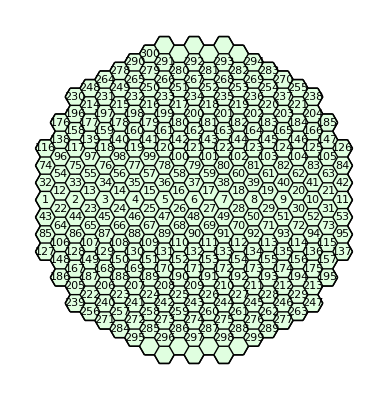

```mathematica
FigA = TemplateCircularHoneycombCover[15];
ShowTissue[FigA, "CellNumbers" -> True]
```

```mathematica
bignet = CelleratorNetwork[FigA, "Reactions" -> net, "Diffusion" -> {{A,DA},{B,DB}}];
```

313 Cells.

6 internal reactions in each cell.

1878 intracellular reactions.

3504 diffusion reactions.

5382 total reactions.

```mathematica
n = NTissueCells[FigA]
```

313

```mathematica
ff[j_]:=Piecewise[{{1,Abs[j-190]<20},{1,Abs[j-280]<20}},0.1]
```

```mathematica
(*Define the initial conditions and parameters*)
```

```mathematica
ic[i_] := {A[i] -> ff[i], B[i] -> ff[i]};
myic = Flatten[ic/@Range[n]];
```

```mathematica
parameters = {DA -> 1, DB -> 1, a-> 0.1, b -> 0.2, c -> 0.1, beta -> 0.1};
```

```mathematica
(*Run Simulation*)
```

```mathematica
sim = RunSim[bignet,parameters,myic,{0,10},MaxSteps -> 100000]
```

{A[1]→InterpolatingFunction[{{0.,10.}},<>],A[2]→InterpolatingFunction[{{0.,10.}},<>],A[3]→InterpolatingFunction[{{0.,10.}},<>],A[4]→InterpolatingFunction[{{0.,10.}},<>],«619»,B[311]→InterpolatingFunction[{{0.,10.}},<>],B[312]→InterpolatingFunction[{{0.,10.}},<>],B[313]→InterpolatingFunction[{{0.,10.}},<>]}

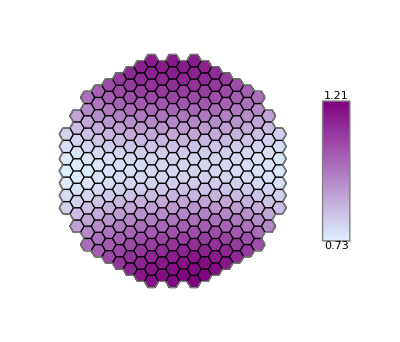

```mathematica
finalpic=SimShowFinal[sim,B,FigA,{LightBlue,Purple}]
```

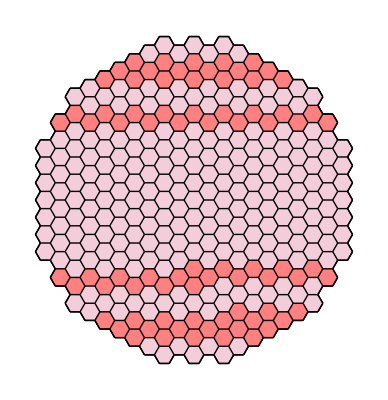

```mathematica
initPic = SimShow[sim,B,0,FigA,{LightPurple, Pink}, {0, .5}]
```